### rule 22 can degenerate into rule 146

```mathematica
init146={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0};
```

```mathematica
init146[[2;;;;2]]
```

{0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,1,0,1,0,1,0,1,0,0,0,1,0}

```mathematica
CellularAutomaton[146,init146[[2;;;;2]],80]===CellularAutomaton[22,init146,{{0,160,2},{1,Length[init146],2}}]
```

True

```mathematica
ArrayPlot[CellularAutomaton[22,init146,160]]
```

-Graphics-

```mathematica
{ArrayPlot[CellularAutomaton[22,init146,{{1,160,2},{2,Length[init146],2}}]],ArrayPlot[CellularAutomaton[22,init146,{{0,160,2},{1,Length[init146],2}}]]}
```

{-Graphics-,-Graphics-}

```mathematica
Union@Flatten@MapIndexed[If[#==1,Mod[#2[[1]],2]+2Mod[#2[[2]],2],4]/4&,CellularAutomaton[146,init146[[2;;;;2]],80],{2}]
```

{0,1/4,1/2,3/4,1}

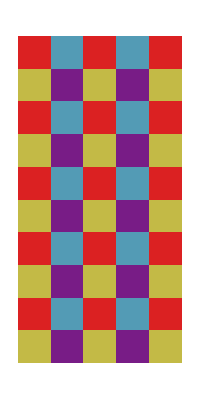

```mathematica
ArrayPlot[Table[(Mod[y,2]+2Mod[x,2])/4,{y,1,10},{x,1,5}],ColorFunction->"Rainbow"]
```

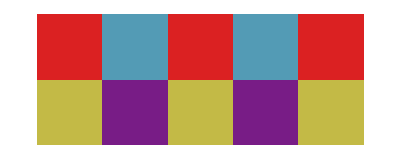

```mathematica
ArrayPlot[Table[(Mod[y,2]+2Mod[x,2])/4,{y,1,2},{x,1,5}],ColorFunction->"Rainbow"]
```

```mathematica
Table[(Mod[y,2]+2Mod[x,2])/4,{y,1,2},{x,1,2}]//TableForm
```

3/4 | 1/4
1/2 | 0

```mathematica
{{"t odd, x odd", "t odd, x even"},{"t even, x odd","t even , x even"}}//TableForm
```

t odd, x odd | t odd, x even
t even, x odd | t even , x even

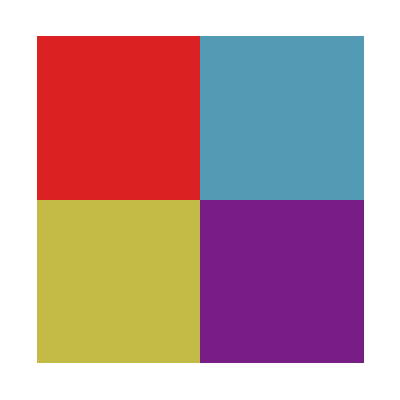

```mathematica
ArrayPlot[Table[(Mod[y,2]+2Mod[x,2])/4,{y,1,2},{x,1,2}],ColorFunction->"Rainbow",PlotLegends->"Expressions"]
```

```mathematica
legend=SwatchLegend[{White,Yellow,Green,Blue,Red},{"t even, x even", "t odd, x even", "t even, x odd", "t odd, x odd", "cell is zero"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"parities",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]
```

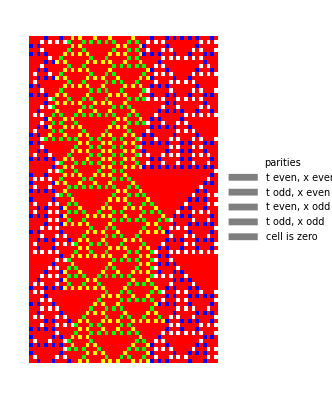

```mathematica
ArrayPlot[MapIndexed[With[{v=#,t=#2[[1]],x=#2[[2]]},If[v==1,Mod[t,2]+2Mod[x,2],4]]&,CellularAutomaton[146,init146[[2;;;;2]],80],{2}],ColorRules->{0->White,1->Yellow,2->Green,3->Blue,4->Red},PlotLegends->legend]
```

### parity regions in rule 146

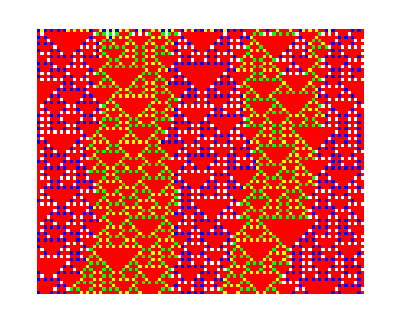

```mathematica
ArrayPlot[MapIndexed[With[{v=#,t=#2[[1]],x=#2[[2]]},If[v==1,Mod[t,2]+2Mod[x,2],4]]&,CellularAutomaton[146,RandomInteger[1,100],80],{2}],ColorRules->{0->White,1->Yellow,2->Green,3->Blue,4->Red}]
```

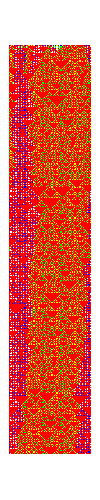
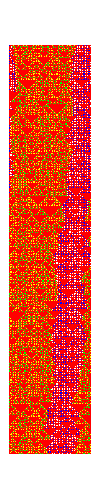
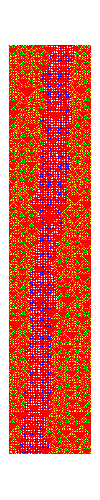
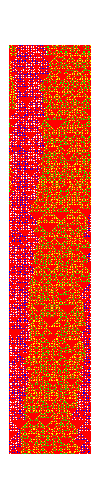

```mathematica
ArrayPlot[#,ColorRules->{0->White,1->Yellow,2->Green,3->Blue,4->Red},PixelConstrained->1]&/@Partition[MapIndexed[With[{v=#,t=#2[[1]],x=#2[[2]]},If[v==1,Mod[t,2]+2Mod[x,2],4]]&,CellularAutomaton[146,RandomInteger[1,100],2000],{2}],500]
```

### parity regions with the appearance of monoliths (large annihilations)

```mathematica
ArrayPlot[MapIndexed[With[{v=#,t=#2[[1]],x=#2[[2]]},If[v==1,Mod[t,2]+2Mod[x,2],4]]&,CellularAutomaton[146,RandomInteger[1,500],1000],{2}],ColorRules->{0->White,1->Yellow,2->Green,3->Blue,4->Red}]
```

-Graphics-

### rule 22 parities are mixed together

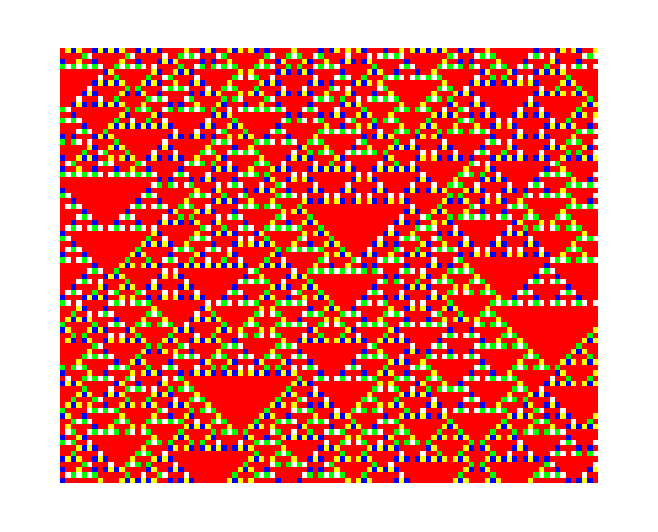

```mathematica
ArrayPlot[MapIndexed[With[{v=#,t=#2[[1]],x=#2[[2]]},If[v==1,Mod[t,2]+2Mod[x,2],4]]&,CellularAutomaton[22,RandomInteger[1,100],80],{2}],ColorRules->{0->White,1->Yellow,2->Green,3->Blue,4->Red}]
```

Rule 146 has distinct regions doing rule 90 on opposite parity lattices, separated by even runs of zeros (particles).
Rule 146 degenerates into one parity of rule 90 when all monoliths are gone (they annihilate each other)

Does rule 22 have interspersed rule 146’s? And after a long time in some cases, only one remains?